Find negative y<-2.0 transition temperature

```mathematica
y=-2.01;
Solve[μ^(-1.0-y)-1.0-μ==0.0,μ]
Clear[y]
```

{{μ→29.1537}}

```mathematica
y=N[-2.0001,100];
μ=NArgMin[{Abs[μ^(-1.0-y)-1.0-μ],μ>1.0},μ]
μ^(-1.0-y)-1.0-μ
Clear[y,μ]
```

1382.33

-4.84783×10^-9

```mathematica
ys=Range[-15.0,-4.0,0.1];
ys=Join[ys,Range[-3.98,-2.1,0.02]];
ys=Join[ys,Range[-2.09,-2.01,0.01]];
ys=Join[ys,Range[-2.009,-2.001,0.001]];
ys
```

{-10.,-9.9,-9.8,-9.7,-9.6,-9.5,-9.4,-9.3,-9.2,-9.1,-9.,-8.9,-8.8,-8.7,-8.6,-8.5,-8.4,-8.3,-8.2,-8.1,-8.,-7.9,-7.8,-7.7,-7.6,-7.5,-7.4,-7.3,-7.2,-7.1,-7.,-6.9,-6.8,-6.7,-6.6,-6.5,-6.4,-6.3,-6.2,-6.1,-6.,-5.9,-5.8,-5.7,-5.6,-5.5,-5.4,-5.3,-5.2,-5.1,-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.98,-3.96,-3.94,-3.92,-3.9,-3.88,-3.86,-3.84,-3.82,-3.8,-3.78,-3.76,-3.74,-3.72,-3.7,-3.68,-3.66,-3.64,-3.62,-3.6,-3.58,-3.56,-3.54,-3.52,-3.5,-3.48,-3.46,-3.44,-3.42,-3.4,-3.38,-3.36,-3.34,-3.32,-3.3,-3.28,-3.26,-3.24,-3.22,-3.2,-3.18,-3.16,-3.14,-3.12,-3.1,-3.08,-3.06,-3.04,-3.02,-3.,-2.98,-2.96,-2.94,-2.92,-2.9,-2.88,-2.86,-2.84,-2.82,-2.8,-2.78,-2.76,-2.74,-2.72,-2.7,-2.68,-2.66,-2.64,-2.62,-2.6,-2.58,-2.56,-2.54,-2.52,-2.5,-2.48,-2.46,-2.44,-2.42,-2.4,-2.38,-2.36,-2.34,-2.32,-2.3,-2.28,-2.26,-2.24,-2.22,-2.2,-2.18,-2.16,-2.14,-2.12,-2.1,-2.09,-2.08,-2.07,-2.06,-2.05,-2.04,-2.03,-2.02,-2.01,-2.009,-2.008,-2.007,-2.006,-2.005,-2.004,-2.003,-2.002,-2.001}

NArgMin::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NArgMin :: cvmit will be suppressed during this calculation.

{0.949928,0.949564,0.949194,0.948819,0.948438,0.948052,0.947659,0.947261,0.946856,0.946446,0.946029,0.945605,0.945174,0.944737,0.944293,0.943841,0.943383,0.942916,0.942442,0.94196,0.94147,0.940971,0.940464,0.939948,0.939423,0.938888,0.938345,0.937791,0.937228,0.936654,0.936069,0.935474,0.934867,0.934249,0.933619,0.932977,0.932322,0.931655,0.930974,0.930279,0.92957,0.928847,0.928108,0.927355,0.926585,0.925798,0.924995,0.924174,0.923335,0.922477,0.921599,0.920702,0.919783,0.918844,0.917881,0.916896,0.915887,0.914853,0.913793,0.912707,0.911592,0.910449,0.909276,0.908072,0.906835,0.905565,0.904259,0.902917,0.901536,0.900116,0.898654,0.897148,0.895597,0.893999,0.89235,0.89065,0.888895,0.887082,0.88521,0.883274,0.881271,0.879199,0.877053,0.874829,0.872523,0.87013,0.867645,0.865064,0.862379,0.859585,0.856675,0.853641,0.850476,0.847171,0.843716,0.8401,0.836313,0.832341,0.828171,0.823787,0.819173,0.814309,0.809175,0.803748,0.798002,0.791906,0.785429,0.778534,0.771176,0.76331,0.754878,0.753118,0.751333,0.749521,0.747683,0.745817,0.743923,0.742,0.740048,0.738066,0.736054,0.734009,0.731933,0.729823,0.727679,0.725501,0.723287,0.721037,0.71875,0.716424,0.714059,0.711653,0.709207,0.706717,0.704184,0.701607,0.698983,0.696313,0.693593,0.690824,0.688003,0.68513,0.682202,0.679219,0.676177,0.673077,0.669915,0.666691,0.663402,0.660045,0.65662,0.653124,0.649554,0.645908,0.642184,0.638378,0.634489,0.630513,0.626447,0.622289,0.618034,0.613679,0.609221,0.604656,0.59998,0.595187,0.590275,0.585238,0.58007,0.574767,0.569324,0.563733,0.557989,0.552085,0.546014,0.539768,0.533338,0.526718,0.519895,0.512862,0.505608,0.49812,0.490386,0.482393,0.474127,0.465571,0.456709,0.447522,0.43799,0.42809,0.417797,0.407084,0.395921,0.384274,0.372105,0.35937,0.34602,0.332,0.317243,0.301673,0.285199,0.267711,0.249073,0.229115,0.207616,0.184276,0.171791,0.158671,0.144828,0.130145,0.114465,0.0975615,0.0790877,0.0584392,0.034301,0.0315844,0.0287888,0.0259035,0.0229145,0.0198031,0.0165426,0.0130922,0.00938172,0.00526119}

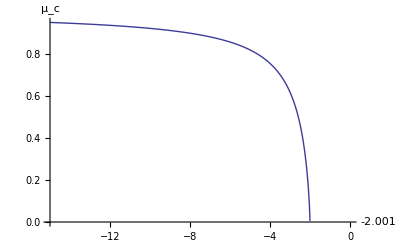

mucVsysFMtrans.csv

```mathematica
Clear[ys]
ys=Range[-15.0,-4.0,0.1];
ys=Join[ys,Range[-3.98,-2.1,0.02]];
ys=Join[ys,Range[-2.09,-2.01,0.01]];
ys=Join[ys,Range[-2.009,-2.001,0.001]];
μinvy=ConstantArray[0,Dimensions[ys][[1]]];
For[ind=1,ind<=Dimensions[ys][[1]],ind+=1,
y=ys[[ind]];
μinvy[[ind]]=1.0/NArgMin[{Abs[μ^(-1.0-y)-1.0-μ],μ>1},μ]
]
μinvy
ListPlot[Table[{ys[[i]],μinvy[[i]]},{i,1,Dimensions[ys][[1]]}],Joined->True,AxesLabel->{y,μ_c}]
Export["mucVsysFMtrans.csv",Transpose[{ys,μinvy}]]
Clear[ys]
```

Find  -2.0<y<2.0<2.2 chaotic transition temperature

```mathematica
Clear[y]
ys=Range[-1.9,1.95,0.005];
μinvy=ConstantArray[0,Dimensions[ys][[1]]];
For[ind=1,ind<=Dimensions[ys][[1]],ind+=1,
μinvy[[ind]]=NArgMin[{Abs[Abs[Jeigfixed[μ,ys[[ind]]]/.{μ->1/x}]-1.0],x>0&&x<0.34},x]
]
μinvy;
Max[Abs[Jeigfixed[1.0/μinvy,ys]]]
ListPlot[Table[{ys[[i]],μinvy[[i]]},{i,1,Dimensions[ys][[1]]}],Joined->True,AxesLabel->{y,μ_c}]
Export["mucVsys4_0005.csv",Transpose[{ys,μinvy}]]
```